```mathematica
real={0.5018, 0.812,
0.7004, 0.6522,
0.8993, 0.5133,
1.0983, 0.3731,
1.2975, 0.2486,
1.4967, 0.153,
1.6961, 0.08873,
1.8956, 0.04845,
2.1376, 0.0226,
2.4374, 0.008365,
2.7777 ,0.002644,
3.1779, 0.0007412,
3.6164 ,0.0001529,
4.1171 ,2.869*10^-05,
4.6543 ,4.296*10^-06,
5.3829, 4.38*10^-07};
```

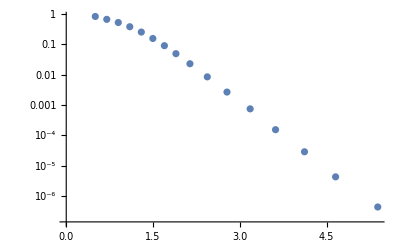

```mathematica
realplot=ListLogPlot[Table[{real[[2i-1]],real[[2i]]},{i,1,16}]]
```

reverse slope T=0.249,Ts=0.327,cS=2.6,cT=38.4,error=  0.507214172727829

```mathematica
Import@SystemDialogInput["FileOpen"]
```

%pt           TTT           TTS           TSS           TSS2j           SSS           SSS2j           Tot
        0.502    6.51825E-01    1.09719E-16    6.52382E-17    8.99695E-19    2.28879E-17    9.14265E-19    6.51825E-01
        0.700    6.18049E-01    6.97290E-17    2.60123E-17    8.13396E-20    2.12552E-17    8.33568E-20    6.18049E-01
        0.899    4.70610E-01    5.10697E-17    1.74080E-17    1.30078E-20    1.95392E-17    1.34499E-20    4.70610E-01
        1.098    3.18142E-01    3.64368E-17    1.25910E-17    2.93339E-21    1.78847E-17    3.06147E-21    3.18142E-01
        1.298    1.99828E-01    2.54924E-17    9.29728E-18    8.33038E-22    1.63625E-17    8.77797E-22    1.99828E-01
        1.497    1.19588E-01    1.77006E-17    6.96087E-18    2.79754E-22    1.49990E-17    2.97697E-22    1.19588E-01
        1.696    6.91597E-02    1.22886E-17    5.27840E-18    1.06628E-22    1.37920E-17    1.14610E-22    6.91597E-02
        1.896    3.90210E-02    8.57325E-18    4.05365E-18    4.49226E-23    1.27298E-17    4.87782E-23    3.90210E-02
        2.138    1.90265E-02    5.60107E-18    2.99235E-18    1.90723E-23    1.15708E-17    2.10943E-23    1.90265E-02
        2.437    7.61039E-03    3.37406E-18    2.09826E-18    6.77068E-24    1.02961E-17    7.61537E-24    7.61039E-03
        2.778    2.62273E-03    1.95446E-18    1.43651E-18    2.37213E-24    9.08668E-18    2.71717E-24    2.62273E-03
        3.178    7.31673E-04    1.06855E-18    9.50166E-19    8.08698E-25    7.95710E-18    9.47260E-25    7.31673E-04
        3.616    1.76996E-04    5.76697E-19    6.26252E-19    2.69825E-25    6.97565E-18    3.20484E-25    1.76996E-04
        4.117    3.43937E-05    3.00971E-19    4.05355E-19    9.46362E-26    6.07184E-18    1.15368E-25    3.43937E-05
        4.654    5.84789E-06    1.58711E-19    2.65085E-19    3.47345E-26    5.28608E-18    4.34943E-26    5.84789E-06
        5.383    5.21133E-07    7.23749E-20    1.57043E-19    1.13002E-26    4.47492E-18    1.49463E-26    5.21133E-07

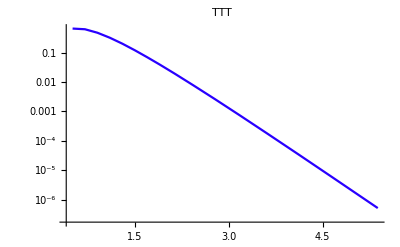
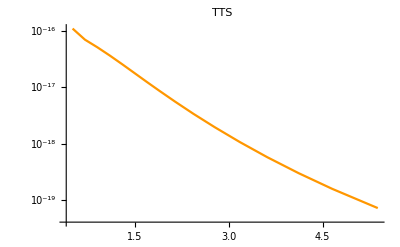
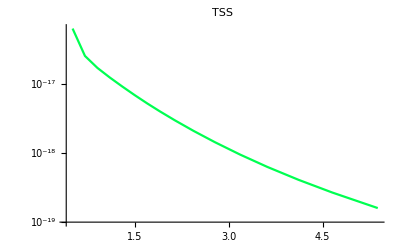
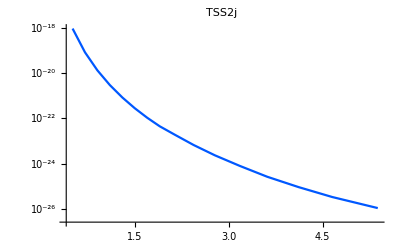
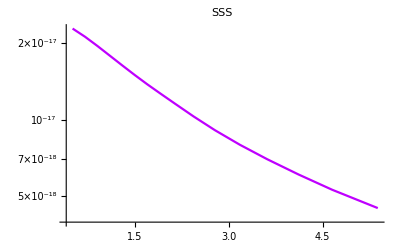
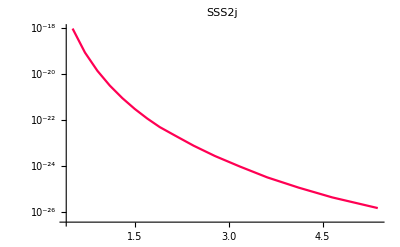
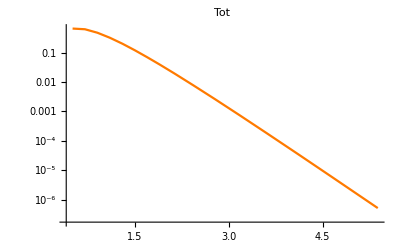

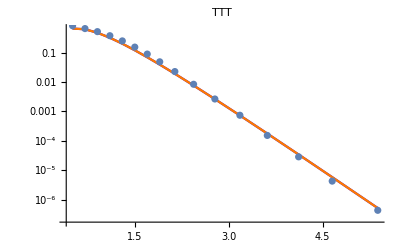

```mathematica
datalabel=StringSplit[StringTrim[StringSplit[%,"\n"][[1]]]];
datalist=StringReplace[#,"E"->"*10^"]&/@ StringSplit[#,"    "]&/@StringSplit[%%,"\n"][[2;;17]]//ToExpression;
Table[ListLogPlot[Join[Partition[datalist[[All,1]],1],Partition[datalist[[All,i]],1],2],PlotLabel->Style[datalabel[[i]],Hue[N@Log[i]]],Joined->True,PlotStyle->Hue[Log@i],PlotRange->Full],{i,2,8}]
Show[{%,realplot}]
```

```mathematica
0.46*(39*10^-3)^0.105
```

0.327205